```mathematica
myred=ColorData[97][4];myblue=ColorData[97][1];myorange=ColorData[97][2];mygreen=ColorData[97][3];
save="C:\\Users\\Leon\\Pictures\\Purcell\\vectorPlot\\";
dataPath="https://raw.githubusercontent.com/muxueqianxun/SuperconductingQubitReadout/main/ReadoutData/";
fontsize=24;font="CMU Sans Serif";
SetOptions[EvaluationNotebook[],StyleDefinitions->Cell[StyleData["GraphicsLabel"],Black,fontsize,FontFamily->font]];
```

## IQ data

```mathematica
dataPathIQ=dataPath<>"IQ/";
data1i=Flatten[Import[dataPathIQ<>"t1i.csv","csv"]];
data1q=Flatten[Import[dataPathIQ<>"t1q.csv","csv"]];
data2i=Flatten[Import[dataPathIQ<>"t2i.csv","csv"]];
data2q=Flatten[Import[dataPathIQ<>"t2q.csv","csv"]];
```

```mathematica
PlotData={data1i,data1q}ᵀ;PlotData1={data2i,data2q}ᵀ;
```

## IQ plot

```mathematica
dataLen=Dimensions[PlotData]⟦1⟧/4;
```

```mathematica
dataG=PlotData⟦1;;0.2*dataLen⟧;
dataE=PlotData⟦dataLen;;1.2*dataLen⟧;
dataF=PlotData⟦2*dataLen;;2.2*dataLen⟧;
dataH=PlotData⟦3*dataLen;;3.2*dataLen⟧;
```

```mathematica
dataNG=Join[Join[dataE,dataF],dataH];
```

```mathematica
dataGMean=Mean[dataG];
dataEMean=Mean[Join[Join[dataE,dataF],dataH]];
dataHMean=Mean[dataH];
```

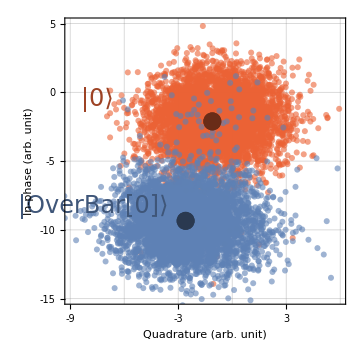

```mathematica
pts=0.012;opa=0.6;
rt1=Show[ListPlot[{dataG,dataH},(*ImageMargins->{{20,0},{0,20}},*)PlotStyle->{{PointSize[pts],myred,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]}},Joined->False,AspectRatio->1,GridLines->{Range[-9,6,3],Range[-15,10,5]},Frame->True,Axes->False,FrameLabel->{{"In-phase (arb. unit)",""},{"Quadrature (arb. unit)","Primary Tone\nReadout Response"}},ImageSize->Medium,PlotRange->{{-9,6},{-15,5}},Epilog->{{Text[Style["|0⟩",fontsize,Darker[myred]],{-7.5,-0.5}]},{Text[Style["|OverBar[0]⟩",fontsize,Darker[myblue]],{-7.7,-8.3}]}},FrameTicks->{{Range[-15,10,5],None},{Range[-9,6,3],None}}],
ListPlot[{{dataGMean},{dataHMean}},PlotStyle->{{PointSize[3*pts],Darker[Darker[myred]]},{PointSize[3*pts],Darker[Darker[myblue]]}}]]
```

```mathematica
dataGtrain=PlotData⟦1;;0.01*dataLen⟧;
dataHtrain=PlotData⟦3*dataLen;;3.01*dataLen⟧;
```

```mathematica
c=Classify[<|0-> dataGtrain,1->dataHtrain|>,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

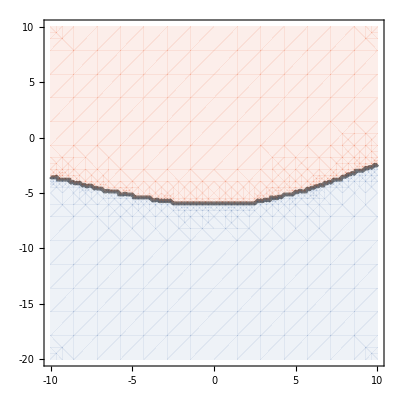

```mathematica
x1=-10;x2=10;y1=-20;y2=10;
xy=Table[{i,j},{i,x1,x2},{j,y1,y2}];
myPiecewise[x_]:=Piecewise[{{Directive[myred,Opacity[0.1]],0≤x<1},{Directive[myblue,Opacity[0.1]],1≤x<2}}]
db=ContourPlot[c[{x,y}],{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Thickness[0.007],Darker[Black]],Contours->1,FrameTicks->{Range[-10,10,5],Range[-20,10,5]}]
```

```mathematica
pge=Select[dataG,c[#]==1&];
```

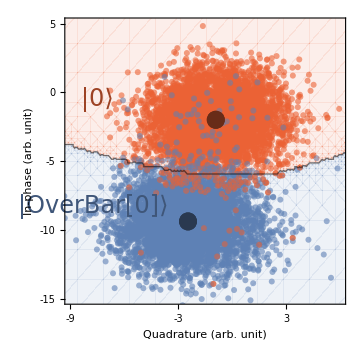

```mathematica
fixSize[plt_,width_,height_]:=Graphics[{Inset[plt]},ImageSize->{width,height},AspectRatio->Full]
g1=fixSize[rt1,360,360]
```

```mathematica
ListPlot[pge,PlotStyle->{PointSize[pts],myred,Opacity[opa]}]
,db,
```

## Gaussian Fit

```mathematica
datagg=Flatten[Import[dataPathIQ<>"data_gg.csv","csv"]];
datage=Flatten[Import[dataPathIQ<>"data_ge.csv","csv"]];
dataeg=Flatten[Import[dataPathIQ<>"data_eg.csv","csv"]];
dataee=Flatten[Import[dataPathIQ<>"data_ee.csv","csv"]];
```

```mathematica
model=A*E^(-(f-μ)^2/σ)
```

A ⅇ^(-(f-μ)^2/σ)

```mathematica
resultgg=NonlinearModelFit[datagg,model,{{A,700},{σ,1100},{μ,15}},f,MaxIterations->1000];
resultgg["BestFitParameters"]
resultge=NonlinearModelFit[datage,model,{{A,700},{σ,1100},{μ,176}},f,MaxIterations->1000];
resultge["BestFitParameters"]
resulteg=NonlinearModelFit[dataeg,model,{{A,700},{σ,1100},{μ,15}},f,MaxIterations->2000];
resulteg["BestFitParameters"]
resultee=NonlinearModelFit[dataee,model,{{A,700},{σ,1100},{μ,176}},f,MaxIterations->2000];
resultee["BestFitParameters"]
```

{A→755.817,σ→346.336,μ→52.3896}

{A→0.256819,σ→2631.74,μ→119.946}

{A→6.42455,σ→379.594,μ→52.7426}

{A→743.246,σ→346.325,μ→139.523}

```mathematica
s1=Mean[{√((σ/.resultgg["BestFitParameters"]⟦2⟧)/2),√((σ/.resultee["BestFitParameters"]⟦2⟧)/2)}]
```

13.1592

```mathematica
cell/s1
```

0.0759923 cell

```mathematica
cell=Length[datagg]
```

200

```mathematica
totalShotsg=Total[Flatten[{datagg,datage}]]
totalShotse=Total[Flatten[{dataeg,dataee}]]
```

24928

24914

```mathematica
mp=Select[Flatten[Position[datagg,0]],#>50&]⟦1⟧
```

96

```mathematica
fg=Round[Total[datagg]/totalShotsg,0.001]//N
fe=Round[Total[dataee]/totalShotse,0.001]//N
fge=Round[Total[datage]/totalShotsg,0.0001]//N
feg=Round[Total[dataeg]/totalShotse,0.0001]//N
fa=Round[Mean[{fg,fe}],0.001]
```

0.999

0.991

0.0009

0.0092

0.995

```mathematica
(*Placed[Framed[LineLegend[{White,White,myred,myorange,mygreen,myblue},{"ℱ_a = "<>ToString[fa],"ℱ_id = "<>ToString[0.9995],"|0|0⟩ = "<>ToString[fg],"|0|0⟩ = "<>ToString[fg],"|1|0⟩ = "<>ToString[fge],"|0|1⟩ = "<>ToString[feg],"|1|1⟩ = "<>ToString[fe]}],Background-> White,FrameMargins-> 0],{Center,Top}]*)
```

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Cell[StyleData["GraphicsLabel"],Black,24]];
```

```mathematica
cell/2
```

100

```mathematica
Table[{i,Round[(i-mp)/s1,1]},{i,-(cell/2+s1*6),(cell/2+s1*12),3*s1}]
```

{{-178.955,-21},{-139.478,-18},{-100.,-15},{-60.5223,-12},{-21.0446,-9},{18.433,-6},{57.9107,-3},{97.3884,0},{136.866,3},{176.344,6},{215.821,9},{255.299,12}}

```mathematica
gridx=Sort[Range[-s1,-5*mp,-s1],Less]~Join~Range[0*mp,5*mp,s1]
```

{-473.732,-460.573,-447.414,-434.255,-421.095,-407.936,-394.777,-381.618,-368.458,-355.299,-342.14,-328.981,-315.821,-302.662,-289.503,-276.344,-263.185,-250.025,-236.866,-223.707,-210.548,-197.388,-184.229,-171.07,-157.911,-144.752,-131.592,-118.433,-105.274,-92.1146,-78.9554,-65.7961,-52.6369,-39.4777,-26.3185,-13.1592,0.,13.1592,26.3185,39.4777,52.6369,65.7961,78.9554,92.1146,105.274,118.433,131.592,144.752,157.911,171.07,184.229,197.388,210.548,223.707,236.866,250.025,263.185,276.344,289.503,302.662,315.821,328.981,342.14,355.299,368.458,381.618,394.777,407.936,421.095,434.255,447.414,460.573,473.732}

```mathematica
framey=Table[{10^i,Superscript[10,i]},{i,-5,-2,1}]
framex=Table[{i,Round[(i-mp)/s1,1]},{i,-(cell/2+s1*6),(cell/2+s1*12),3*s1}]
```

{{1/100000,10^-5},{1/10000,10^-4},{1/1000,10^-3},{1/100,10^-2}}

{{-178.955,-21},{-139.478,-18},{-100.,-15},{-60.5223,-12},{-21.0446,-9},{18.433,-6},{57.9107,-3},{97.3884,0},{136.866,3},{176.344,6},{215.821,9},{255.299,12}}

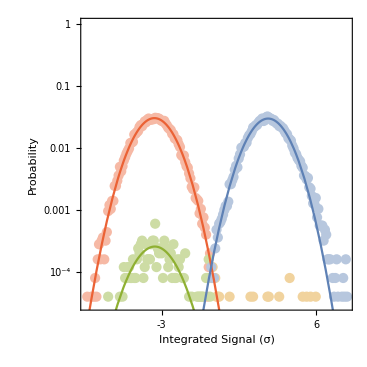

C:\Users\Leon\Pictures\Purcell\vectorPlot\gaussian.pdf

C:\Users\Leon\Pictures\Purcell\vectorPlot\gaussian.pdf

```mathematica
thi=0.02;fs=16;
fitplotg=Legended[Show[ListLogPlot[{datagg/totalShotsg,datage/totalShotsg,dataeg/totalShotse,dataee/totalShotse},ImageSize-> 367,(*ImageMargins->{{20,0},{0,20}},*)Joined->False,PlotRange->{{0.00003,1}},Frame->True,PlotStyle->{{Lighter[Lighter[myred]],PointSize[thi]},{Lighter[Lighter[myorange]],PointSize[thi]},{Lighter[Lighter[mygreen]],PointSize[thi]},{Lighter[Lighter[myblue]],PointSize[thi]}},AspectRatio->1,FrameLabel->{{"Probability",""},{"Integrated Signal (σ)","Two-state ℱ_a = "<>ToString[100*0.995]<>"%"<>"\nIdeal ℱ_id = "<>ToString[100*0.9995]<>"%"}},FrameTicks->{{framey,None},{framex,None}},GridLines->{framex⟦All,1⟧,Full}],LogPlot[{resultgg[t]/totalShotsg,0*resultge[t]/totalShotsg,resulteg[t]/totalShotse,resultee[t]/totalShotse},{t,0,Length[datagg]},PlotStyle-> {myred,myorange,mygreen,myblue},PlotRange->All,Exclusions->None]],{(*Placed[Framed[PointLegend[{White,White},{"ℱ_a = "<>ToString[fa],"ℱ_id = "<>ToString[0.9995]},LegendMargins->2],Background-> White,FrameMargins-> 0],{Center,Top}],*)
Placed[Framed["                                  

",Background-> White,FrameMargins->7.5,FrameStyle->{Gray,Thin}],{0.5,0.85}],Placed[Framed[PointLegend[{myred,mygreen},{Style["P(0|0) = "<>ToString[100*fg]<>"%",FontSize->fs,FontFamily->font],Style["P(0|OverBar[0]) = "<>ToString[100*feg]<>"%",FontSize->fs,FontFamily->font]},LegendMargins->0],Background-> Transparent,FrameMargins-> 0,FrameStyle->Transparent],{0.26,0.85}],Placed[Framed[PointLegend[{myblue,myorange},{Style["P(OverBar[0]|OverBar[0]) = "<>ToString[100*fe]<>"%",FontSize->fs,FontFamily->font],Style["P(OverBar[0]|0) = "<>ToString[100*fge]<>"%",FontSize->fs,FontFamily->font]},LegendMargins->0],Background-> Transparent,FrameMargins-> 0,FrameStyle->Transparent],{0.742,0.86}]}]
Export[save<>"gaussian.pdf",fitplot]
```

```mathematica
{(*Placed[Framed[PointLegend[{White,White},{"ℱ_a = "<>ToString[fa],"ℱ_id = "<>ToString[0.9995]},LegendMargins->2],Background-> White,FrameMargins-> 0],{Center,Top}],*)
Placed[Framed["                                      

",Background-> White,FrameMargins->10,FrameStyle->Black],{0.495,0.87}],Placed[Framed[PointLegend[{myred,myorange},{Style["P(0|0) = "<>ToString[100*fg]<>"%",FontSize->16],Style["P(OverBar[0]|0) = "<>ToString[100*fge]<>"%",FontSize->16]},LegendMargins->2.5],Background-> Transparent,FrameMargins-> 0,FrameStyle->White],{0.25,0.85}],Placed[Framed[PointLegend[{mygreen,myblue},{Style["P(0|OverBar[0]) = "<>ToString[100*feg]<>"%",FontSize->16],Style["P(OverBar[0]|OverBar[0]) = "<>ToString[100*fe]<>"%",FontSize->16]},LegendMargins->2.5],Background-> Transparent,FrameMargins-> 0,FrameStyle->White],{0.748,0.86}]}
```

{Placed[                                      

,{0.495,0.87}],Placed[,{0.25,0.85}],Placed[,{0.748,0.86}]}

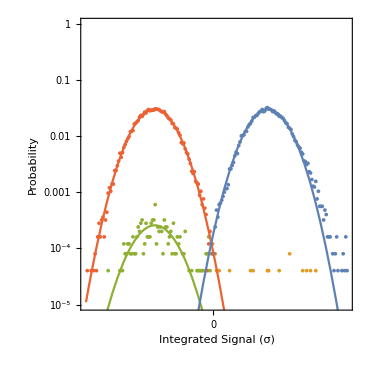

C:\Users\Leon\Pictures\Purcell\vectorPlot\gaussianppt.png

```mathematica
fitplot=Legended[Show[ListLogPlot[{datagg/totalShotsg,datage/totalShotsg,dataeg/totalShotse,dataee/totalShotse},ImageSize-> 367,Joined->False,PlotRange->{{0.00001,1}},Frame->True,PlotStyle->{myred,myorange,mygreen,myblue},AspectRatio->1,FrameLabel->{{"Probability",""},{"Integrated Signal (σ)","Two-state ℱ_a = "<>ToString[100*fa]<>"%"<>"\nIdeal ℱ_id = "<>ToString[100*0.9995]<>"%"}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,-1,1}],None},{Table[{i,Round[(i-mp)/s1,1]},{i,-(cell/2+s1*15),(cell/2+s1*15),2*s1}],None}},GridLines->{Table[i,{i,0,2*mp,mp}],Full}],LogPlot[{resultgg[t]/totalShotsg,0*resultge[t]/totalShotsg,resulteg[t]/totalShotse,resultee[t]/totalShotse},{t,0,Length[datagg]},PlotStyle-> {myred,myorange,mygreen,myblue},PlotRange->All,Exclusions->None]],{(*Placed[Framed[PointLegend[{White,White},{"ℱ_a = "<>ToString[fa],"ℱ_id = "<>ToString[0.9995]},LegendMargins->2],Background-> White,FrameMargins-> 0],{Center,Top}],*)Placed[Framed[PointLegend[{myred,myorange,mygreen,myblue},{Style["P(0|0) = "<>ToString[100*fg]<>"%",FontSize->20],Style["P(OverBar[0]|0) = "<>ToString[100*fge]<>"%",FontSize->20],Style["P(0|OverBar[0]) = "<>ToString[100*feg]<>"%",FontSize->20],Style["P(OverBar[0]|OverBar[0]) = "<>ToString[100*fe]<>"%",FontSize->20]},LegendMargins->5.5],Background-> White,FrameMargins-> 0],{Center,Top}]}]
Export[save<>"gaussianppt.png",fitplot]
```

```mathematica
Export[save<>"rt1.png",rt1]
```

C:\Users\Leon\Pictures\Purcell\vectorPlot\rt1.png

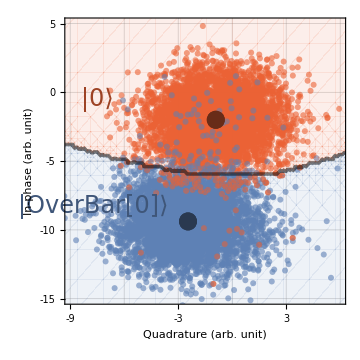
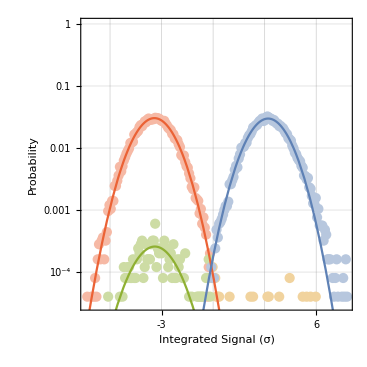

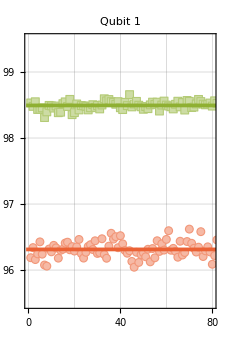
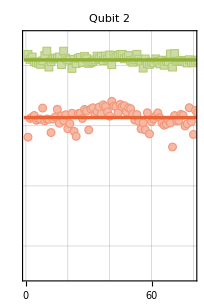
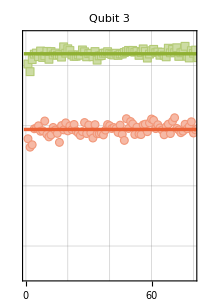
-Graphics--Graphics--Graphics-Measurement NumberAssignment   Fidelity ℱ_a

```mathematica
plotAll=Row[{rt1,fitplotg}]
plotAllAverage
```

```mathematica
Export[save<>"iqt1.png",plotAll]
```

C:\Users\Leon\Pictures\Purcell\vectorPlot\iqt1.png

## IQ Data

```mathematica
dataPathIQ=dataPath<>"IQ/";
calib1i=Flatten[Import[dataPathIQ<>"t1i_gefh_calib.csv","csv"]];
calib1q=Flatten[Import[dataPathIQ<>"t1q_gefh_calib.csv","csv"]];
calib2i=Flatten[Import[dataPathIQ<>"t2i_gefh_calib.csv","csv"]];
calib2q=Flatten[Import[dataPathIQ<>"t2q_gefh_calib.csv","csv"]];
data1i=Flatten[Import[dataPathIQ<>"t1i_gef_data.csv","csv"]];
data1q=Flatten[Import[dataPathIQ<>"t1q_gef_data.csv","csv"]];
data2i=Flatten[Import[dataPathIQ<>"t2i_gef_data.csv","csv"]];
data2q=Flatten[Import[dataPathIQ<>"t2q_gef_data.csv","csv"]];
data1ipre=Flatten[Import[dataPathIQ<>"t1i_gef_data_pre.csv","csv"]];
data1qpre=Flatten[Import[dataPathIQ<>"t1q_gef_data_pre.csv","csv"]];
data2ipre=Flatten[Import[dataPathIQ<>"t2i_gef_data_pre.csv","csv"]];
data2qpre=Flatten[Import[dataPathIQ<>"t2q_gef_data_pre.csv","csv"]];
```

## Two-Tone readout with Neural Network

```mathematica
Clear[ThresholdData,FindCM] 
ThresholdData[countProb_,thres_]:=Module[{},gselect=(Max[#]>thres⟦1⟧)&/@(Flatten[Values[countProb⟦1⟧]]);
eselect=(Max[#]>thres⟦2⟧)&/@(Flatten[Values[countProb⟦2⟧]]);
fselect=(Max[#]>thres⟦3⟧)&/@(Flatten[Values[countProb⟦3⟧]]);
{gselect,eselect,fselect}]
FindCM[count_,select_,preselect_,plot_:False]:=Module[{},gselectFinal=Thread[And[select⟦1⟧,preselect⟦1⟧]];
eselectFinal=Thread[And[select⟦2⟧,preselect⟦2⟧]];
fselectFinal=Thread[And[select⟦3⟧,preselect⟦3⟧]];
gcountFinal=Pick[count⟦1⟧,gselectFinal];ecountFinal=Pick[count⟦2⟧,eselectFinal];fcountFinal=Pick[count⟦3⟧,fselectFinal];
cag=Flatten[Count[gcountFinal,#](*/Dimensions[gcountFinal]*)&/@{0,1,2,3}];
cag=cag⟦1;;2⟧~Join~{Total[cag⟦3;;4⟧]}//N;
cae=Flatten[Count[ecountFinal,#](*/Dimensions[ecountFinal]*)&/@{0,1,2,3}];
cae={cae⟦1⟧}~Join~{Total[cae⟦3;;4⟧]}~Join~{cae⟦2⟧}//N;
caf=Flatten[Count[fcountFinal,#](*/Dimensions[fcountFinal]*)&/@{0,1,2,3}];
caf={caf⟦1⟧}~Join~{Total[caf⟦3;;4⟧]}~Join~{caf⟦2⟧}//N;
cm={cag,cae,caf};
cmNorm={cag/Dimensions[gcountFinal]⟦1⟧,cae/Dimensions[ecountFinal]⟦1⟧,caf/Dimensions[fcountFinal]⟦1⟧};
If[plot,
Print[Mean[Diagonal[cm]],cm//MatrixForm,Mean[Diagonal[cmNorm]],cmNorm//MatrixForm]];
{cm,cmNorm}]
```

```mathematica
calibAll={calib1i,calib1q,calib2i,calib2q}ᵀ;
dataAll={data1i,data1q,data2i,data2q}ᵀ;
preData={data1ipre,data1qpre,data2ipre,data2qpre}ᵀ;
dataLen=Dimensions[PlotData]⟦1⟧/4;
calibG=calibAll⟦1;;1*dataLen⟧;
calibE=calibAll⟦dataLen+1;;2*dataLen⟧;
calibF=calibAll⟦2*dataLen+1;;3*dataLen⟧;
calibH=calibAll⟦3*dataLen+1;;4*dataLen⟧;
sample=5000;
calibGSample=RandomSample[calibG,sample];
calibESample=RandomSample[calibE,sample];
calibFSample=RandomSample[calibF,sample];
calibHSample=RandomSample[calibH,sample];
```

```mathematica
trainingData=Flatten[{#-> 0&/@calibGSample,#-> 1&/@calibESample,#-> 3&/@calibHSample}];
net=NetChain[{LinearLayer[32],ElementwiseLayer[Ramp],LinearLayer[3],SoftmaxLayer[]},"Input"->{4},"Output"->NetDecoder[{"Class",{0,1,3}}]];
Information[net,"SummaryGraphic"]
```

-Graphics-

```mathematica
results=NetTrain[net,trainingData,All]
trained=results["TrainedNet"]
```

NetTrain Results
summary | ,,  batches:40420  rounds:172  time:47s  examples/s:55234
data | ,,  training examples:15000  processed examples:2586880  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.45×10^-1  error:3.11%
 | 
 |

NetChain[<>]

```mathematica
dataGpre=preData⟦1;;1*dataLen⟧;
dataEpre=preData⟦dataLen+1;;2*dataLen⟧;
dataFpre=preData⟦2*dataLen+1;;3*dataLen⟧;
dataG=dataAll⟦1;;1*dataLen⟧;
dataE=dataAll⟦dataLen+1;;2*dataLen⟧;
dataF=dataAll⟦2*dataLen+1;;3*dataLen⟧;
```

```mathematica
c=trained;
gprecountProb=c[dataGpre,"Probabilities"];
eprecountProb=c[dataEpre,"Probabilities"];
fprecountProb=c[dataFpre,"Probabilities"];
precountProb ={gprecountProb,eprecountProb,fprecountProb};
gcountProb=MaximalBy[1]@# &/@c[dataG,"Probabilities"];
ecountProb=MaximalBy[1]@# &/@c[dataE,"Probabilities"];
fcountProb=MaximalBy[1]@# &/@c[dataF,"Probabilities"];
gcount=Flatten[Keys[gcountProb]];ecount=Flatten[Keys[ecountProb]];fcount=Flatten[Keys[fcountProb]];
countProb ={gcountProb,ecountProb,fcountProb};
count = {gcount,ecount,fcount};
```

```mathematica
threspre=Table[0.5,3];
preselect=ThresholdData[precountProb,threspre];
```

```mathematica
thresSweep=Range[0.8,0.99,0.005];
cmList={};cmfList={};
Do[thres=thresSweep⟦i⟧;
select=ThresholdData[countProb,Table[thres,3]];
cms=FindCM[count,select,preselect];
AppendTo[cmList,cms⟦1⟧];
AppendTo[cmfList,cms⟦2⟧];
,{i,1,Dimensions[thresSweep]⟦1⟧}]
```

```mathematica
cmPlotList={};thresList={};cutoff=0.9;
Do[cmMax=Max[#]&/@(cmList⟦All,i⟧ᵀ);
cmPlot={Table[thresSweep,3],cmList⟦All,i⟧ᵀ/cmMax}ᵀ;
cmPlot=#ᵀ&/@cmPlot;cmPlot⟦i⟧;
thresIdx=Nearest[cmPlot⟦i⟧⟦All,2⟧-> "Index",cutoff];
thresPt=thresSweep⟦thresIdx⟦1⟧⟧;
AppendTo[cmPlotList,cmPlot];AppendTo[thresList,thresPt];
(*Print[ListPlot[cmPlot,Joined->True,PlotRange-> {0.7,1}]];*)
,{i,1,3}]
```

```mathematica
select=ThresholdData[countProb,thresList];
cms=FindCM[count,select,preselect,plot=True];
```

21338.(21624. | 6. | 9.
65. | 21057. | 586.
628. | 398. | 21333.)0.974477(0.999307 | 0.000277277 | 0.000415916
0.00299429 | 0.970011 | 0.0269947
0.0280871 | 0.0178004 | 0.954112)

## CM Plot

```mathematica
m=Round[cms⟦2⟧*100,0.01];
a=50;max=100;
cf=Opacity[1-a^(-#/max),myblue]&;
fa=Round[Mean[Diagonal[cms⟦2⟧*100]],0.01];
t=Transpose@Map[Flatten,{#,Reverse@Transpose@#}&[Table[Range[1,2 #-1,2],{#}]]&[Length@m]]/2;
```

```mathematica
ml=Round[cms⟦2⟧*100,100];
legendPlot=Show[MatrixPlot[ml,(*ImageMargins->{{20,0},{0,20}},*)ImageSize->{120,350},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->fontsize,FontFamily->font],Right,Rotate[#,90 Degree]&]],{1,0.5}]],MatrixPlot[ml,Epilog->Style[Text@@@Transpose[{Catenate@ml,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->350,ColorFunction->cf,ColorFunctionScaling->False]
];
cm0Plot=Show[MatrixPlot[m,Epilog->MapIndexed[Text[Style[Round[#,.01],fontsize,If[Abs[#]≥50,White,Black],FontFamily->font],{#2[[1]],4-#2[[2]]}-.5]&,mplot,{2}],(*ImageMargins->{{20,0},{0,20}},*)FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->{460,350},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},(*PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->24],Right,Rotate[#,90 Degree]&]],{1,0.5}],*)FrameLabel->{ "Prepared State","Measured State","",Style["Three-state Readout\n Assignment Fidelity ℱ_a = "<>ToString[fa]<>"%",fontsize]}],MatrixPlot[m,Epilog->Style[Text@@@Transpose[{Catenate@m,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->352,ColorFunction->cf,ColorFunctionScaling->False]];
Show[cm0Plot,legendPlot]
```

-Graphics-

## IQ Plot

```mathematica
x1=-9;x2=6;y1=-15;y2=5;
xy1=Table[{i,j},{i,x1,x2},{j,y1,y2}];
d=Dimensions[xy1];
```

```mathematica
dataGMeant2=Mean[dataG]⟦3;;4⟧;
dataEMeant2=Mean[dataE]⟦3;;4⟧;
dataFMeant2=Mean[dataF]⟦3;;4⟧;
datat2=Mean[{dataGMeant2,dataEMeant2,dataFMeant2}];
```

```mathematica
myPiecewise[x_]:=Piecewise[{{Directive[myred,Opacity[0.1]],0≤x<1},{Transparent,1≤x<2}}]
cp11=ContourPlot[c[{x,y,datat2⟦1⟧,datat2⟦2⟧}]/.{2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myblue,Opacity[0.1]],1≤x<2}}]
cp41=ContourPlot[c[{x,y,datat2⟦1⟧,datat2⟦2⟧}]/.{1->1,2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
```

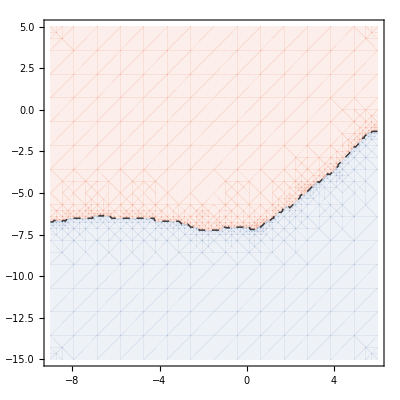

```mathematica
dbt1=Show[cp11,cp41]
```

```mathematica
sample1=2500;
dataGSamplet1=RandomSample[dataG,sample1]⟦All,1;;2⟧;
dataESamplet1=RandomSample[dataE,sample1]⟦All,1;;2⟧;
dataFSamplet1=RandomSample[dataF,sample1]⟦All,1;;2⟧;
```

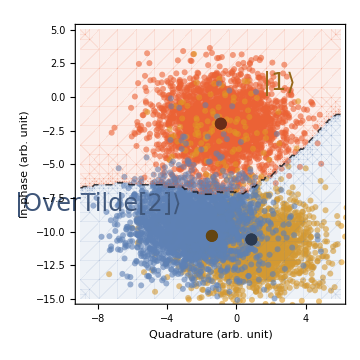

```mathematica
pts=0.012;opa=0.6;
rt21=Show[ListPlot[{dataGSamplet1,dataFSamplet1,dataESamplet1},PlotStyle->{{PointSize[pts],myred,Opacity[opa]}(*,{PointSize[pts],mygreen,Opacity[opa]}*),{PointSize[pts],myorange,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]}},Joined->False,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{{"In-phase (arb. unit)"(*""*),""},{"Quadrature (arb. unit)","Secondary Tone\nReadout Reponse"}},ImageSize->Medium,PlotRange->{{-9,6},{-15,5}},Epilog->{{Text[Style["|0⟩",24,Darker[myred]],{-0.5,6}]},{Text[Style["|OverTilde[2]⟩",24,Darker[myblue]],{-8,-8}]},{Text[Style["|1⟩",24,Darker[myorange]],{2.5,1}]}}],dbt1,
ListPlot[{{dataGMeant1},{dataEMeant1},{dataFMeant1}(*{dataFMean1},{dataHMean1}*)},PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]}(*,{PointSize[2*pts],Darker[Darker[mygreen]]}*),{PointSize[2*pts],Darker[Darker[myblue]]},{PointSize[2*pts],Darker[Darker[myorange]]}}]]
```

```mathematica
dataGMeant1=Mean[calibG]⟦1;;2⟧;
dataEMeant1=Mean[calibE]⟦1;;2⟧;
dataFMeant1=Mean[calibF]⟦1;;2⟧;
datat1=Mean[{dataGMeant1,dataEMeant1}];
```

```mathematica
myPiecewise[x_]:=Piecewise[{{Directive[myred,Opacity[0.1]],0≤x<1},{Transparent,1≤x<2}}]
cp11=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myorange,Opacity[0.1]],1≤x<2}}]
cp21=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{2->0,3->0},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myblue,Opacity[0.1]],1≤x<2}}]
cp41=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{1->0,2->0,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
```

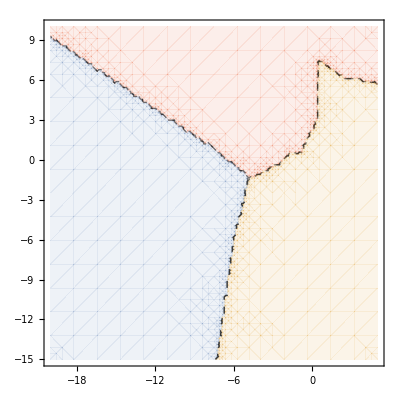

```mathematica
dbt2=Show[cp11,cp21,cp41]
```

```mathematica
sample1=2500;
dataGSample1=RandomSample[dataG,sample1]⟦All,3;;4⟧;
dataESample1=RandomSample[dataE,sample1]⟦All,3;;4⟧;
dataFSample1=RandomSample[dataF,sample1]⟦All,3;;4⟧;
```

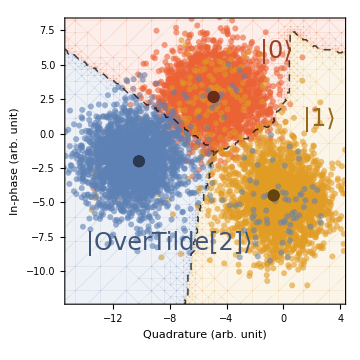

```mathematica
pts=0.012;opa=0.6;
rt21=Show[ListPlot[{dataGSample1,dataFSample1,dataESample1},PlotStyle->{{PointSize[pts],myred,Opacity[opa]}(*,{PointSize[pts],mygreen,Opacity[opa]}*),{PointSize[pts],myorange,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]}},Joined->False,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{{"In-phase (arb. unit)"(*""*),""},{"Quadrature (arb. unit)","Secondary Tone\nReadout Reponse"}},ImageSize->Medium,PlotRange->{{-15,4},{8-20,8}},Epilog->{{Text[Style["|0⟩",24,Darker[myred]],{-0.5,6}]},{Text[Style["|OverTilde[2]⟩",24,Darker[myblue]],{-8,-8}]},{Text[Style["|1⟩",24,Darker[myorange]],{2.5,1}]}}],db11,
ListPlot[{{dataGMeant2},{dataEMeant2},{dataFMeant2}(*{dataFMean1},{dataHMean1}*)},PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]}(*,{PointSize[2*pts],Darker[Darker[mygreen]]}*),{PointSize[2*pts],Darker[Darker[myblue]]},{PointSize[2*pts],Darker[Darker[myorange]]}}]]
```

```mathematica
dataGMeant2=Mean[dataG]⟦3;;4⟧
dataEMeant2=Mean[dataE]⟦3;;4⟧
dataFMeant2=Mean[dataF]⟦3;;4⟧
datat2=Mean[{dataGMeant2,dataEMeant2,dataFMeant2}]
```

{-4.90674,2.66526}

{-10.1625,-2.01322}

{-0.681157,-4.49674}

{-5.25015,-1.28157}